# MATH 263 Numerical differential equations

Ethan Smith

## Lecture 2: Euler’s method 11 FEB 2021

## Assigned reading for next time.

Zill, Section 9.1.

## Method implementations.

```mathematica
euler[f_,a_,b_,y0_,n_]:=Module[{x,y,h},
{x[0],y[0]} = {a,y0};
h=N[(b-a)/n];
Do[
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*f[x[i],y[i]];,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]]
];
```

## Euler’s method.

Suppose that we want to numerically solve a first order IVP

y’ = f(x,y), y(x_0) = y_0

over some interval [a,b].  Choosing some positive integer n, our goal is compute a set (or table) of points (x_i,y_i) so that if y is the true solution, then

y(x_i)≈ y_i

for  i = 0,1,..., n.  We say that there are n steps, or equivalently n+1 mesh points or nodes.  The distance h_i=x_(i+1)-x_i is called the ith step-size, which may be variable.  For much of the course, however, we will use a fixed step size h=(b-a)/n.

Once the mesh points have been chosen, the most straightforward approach to computing the y_i’s is known as Euler’s method, which simply appeals to the calc I idea of linearization.  Namely, if y is the true solution and we assume that we have y_i=y(x_i) exactly, then we have the approximation

y(x_(i+1))≈ y(x_i) + dy/dx(x_(i+1) - x_i)
			           = y_i + f(x_i,y_i)h.

Euler’s method is to recursively define the y_i by the formula

y_(i+1)= y_i + f(x_i,y_i)h.

for i = 0, 1,...,n.  Note that y_0 = y(x_0) exactly.

Consider the IVP y' = x^2 - y, y(0)=3.

Solve the IVP with DSolve, and extract the solution (as a function), calling it trueY.

```mathematica
Clear[x,y] (* In this cell, we want to use the symbols x, y as indeterminate "place holder" symbols.  It is a good idea make sure that symbols are clear before proceeding. *)
f[x_,y_]=x^2-y;
{x0,y0}={0,3};
trueY[x_]=y[x]/.DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x][[1]];
StringForm["The true solution to the IVP is ``.", TraditionalForm[y[x]==trueY[x]]]
```

The true solution to the IVP is y(x)==ⅇ^-x (ⅇ^x x^2-2 ⅇ^x x+2 ⅇ^x+1).

Solve the IVP on the interval [0,2] using Euler’s method with n=20.  Display the graph of the exact solution on the interval [0,2] along with the points for the approximate solution.

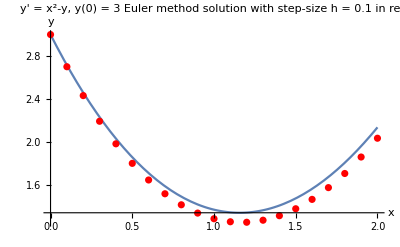

```mathematica
{a,b}={0,2};
n=20;
h=N[(b-a)/n];
Show[
Plot[trueY[x],{x,a,b}],
ListPlot[euler[f,a,b,y0,n],PlotStyle->Red],
PlotLabel->StringForm["y' = ``, y(``) = ``\n Euler method solution with step-size h = `` in red",f[x,y],x0,y0,h],PlotRange->All, AxesLabel->{x,y}
]
```

Consider the IVP y' = x + y, y(0) = 1.

Find the exact solution with DSolve.

```mathematica
Clear[x,y]
f[x_,y_]=x+y;
{x0,y0}={0,1};
trueY[x_]=y[x]/.DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x][[1]];
StringForm["The true solution to the IVP is ``.", TraditionalForm[y[x]==trueY[x]]]
```

The true solution to the IVP is y(x)==-x+2 ⅇ^x-1.

Use your implementation of Euler’s method to solve the IVP with n=10 and n=20 to approximate the solution over the interval [0,1].

```mathematica
{a,b}={0,1};
eulerSoln10=euler[f,a,b,y0,10]
eulerSoln20=euler[f,a,b,y0,20]
```

{{0,1},{0.1,1.1},{0.2,1.22},{0.3,1.362},{0.4,1.5282},{0.5,1.72102},{0.6,1.94312},{0.7,2.19743},{0.8,2.48718},{0.9,2.8159},{1.,3.18748}}

{{0,1},{0.05,1.05},{0.1,1.105},{0.15,1.16525},{0.2,1.23101},{0.25,1.30256},{0.3,1.38019},{0.35,1.4642},{0.4,1.55491},{0.45,1.65266},{0.5,1.75779},{0.55,1.87068},{0.6,1.99171},{0.65,2.1213},{0.7,2.25986},{0.75,2.40786},{0.8,2.56575},{0.85,2.73404},{0.9,2.91324},{0.95,3.1039},{1.,3.3066}}

Plot the true solution and the two approximate solutions together on a single set of axes.  This time use ListPlot’s Joined and Mesh options to connect the dots.  What do you observe?

```mathematica
Show[
Plot[trueY[x],{x,a,b},PlotStyle->Black,PlotLabels->"true solution"],
ListPlot[{eulerSoln10,eulerSoln20},Joined->True,PlotLegends->{"n = 10", "n = 20"},Mesh->All],
PlotLabel->StringForm["y' = ``, y(``) = ``\n Euler method solutions with different step-sizes",f[x,y],x0,y0,h], AxesLabel->{x,y}
]
```

-Graphics-

The solution with more points (higher n), or equivalently smaller step-size (smaller h) yields a more accurate approximation.

Compare the values of the approximations with the true solution at x=1.  Compute both absolute and relative errors.

```mathematica
absError10=Abs[trueY[1]-Last[eulerSoln10][[2]]];
relError10=absError10/Abs[trueY[1]];
Print[StringForm["When n = ``, the absolute error is `` while the relative error is ``.", 10, absError10, relError10]]

absError20=Abs[trueY[1]-Last[eulerSoln20][[2]]];
relError20=absError20/Abs[trueY[1]];
Print[StringForm["When n = ``, the absolute error is `` while the relative error is ``.", 20, absError20, relError20]]
```

When n = 10, the absolute error is 0.249079 while the relative error is 0.072479.

When n = 20, the absolute error is 0.129968 while the relative error is 0.0378192.

Run Euler’s method again with n=100 and n=1000 on the interval [0,10].  Compare each to the true solution by plotting their graphs together.

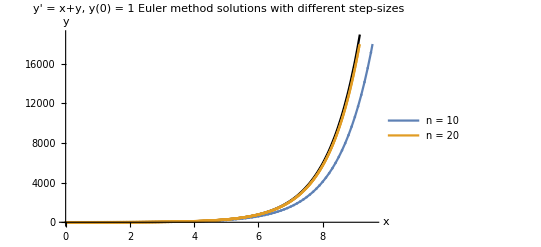

```mathematica
{a,b}={0,10};
eulerSoln100=euler[f,a,b,y0,100];
eulerSoln1000=euler[f,a,b,y0,1000];

Show[
Plot[trueY[x],{x,a,b},PlotStyle->Black],
ListPlot[{eulerSoln100,eulerSoln1000},Joined->True,PlotLegends->{"n = 10", "n = 20"},Mesh->All],
PlotLabel->StringForm["y' = ``, y(``) = ``\n Euler method solutions with different step-sizes",f[x,y],x0,y0,h], AxesLabel->{x,y},PlotRange->All
]
```